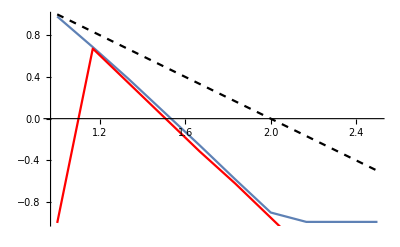

```mathematica
Clear["Global`*"];

gamma = 0;
mu = 0;

sigma = 0.2;


numr = 10;
rmin = 1.00001; 
rmax = 2.5;
rvec = Table[r,{r, rmin, rmax, (rmax - rmin)/(numr -1)}];
critomvec = Table[0, {r, rmin, rmax, (rmax - rmin)/(numr -1)}];
critl1vec = Table[0, {r, rmin, rmax, (rmax - rmin)/(numr -1)}];


w0funct[mydelta_] := 0.5(1.0 + Erf[mydelta/Sqrt[2.0]]);
w1funct[mydelta_] := 0.5 (Sqrt[2.0/Pi]Exp[-mydelta^2/2.0]+ mydelta (1.0 + Erf[mydelta/Sqrt[2]]));
w2funct[mydelta_] := w0funct[mydelta] + mydelta w1funct[mydelta];


effinf  = 1000;
eps = 0.00001;
Monitor[For[i = 1, i<numr+1, i++,
r = rvec[[i]];
numom = 100;
ommin = -0.99; 
ommax = 2-r ;
omvec = Table[myom,{myom, ommin, ommax, (ommax - ommin)/(numom -1)}];
numom = 100;
ommin = -10; 
ommax =0;
l1vec = Table[myom,{myom, ommin, ommax, (ommax - ommin)/(numom -1)}];
fvec = Table[0,{myom, ommin, ommax, (ommax - ommin)/(numom -1)}];
fvec2 = Table[0,{myom, ommin, ommax, (ommax - ommin)/(numom -1)}];
For[j= 1, j<numom+1, j++,
om= omvec[[j]];
l1 = l1vec[[j]];


start =10.0;

(*Solving for the delta *)
sol = FindRoot[{sigma^2 ((1+gamma)( 0.5(1.0 + Erf[mydelta/Sqrt[2.0]])) + mydelta ( 0.5 (Sqrt[2.0/Pi]Exp[-mydelta^2/2.0]+ mydelta (1.0 + Erf[mydelta/Sqrt[2]]))))^2==( ( 0.5(1.0 + Erf[mydelta/Sqrt[2.0]])) + mydelta ( 0.5 (Sqrt[2.0/Pi]Exp[-mydelta^2/2.0]+ mydelta (1.0 + Erf[mydelta/Sqrt[2]]))))},{mydelta, start}];
{delta} = {mydelta} /.sol;
w0 = 0.5(1.0 + Erf[delta/Sqrt[2.0]]);
w1 = 0.5 (Sqrt[2.0/Pi]Exp[-delta^2/2.0]+ delta (1.0 + Erf[delta/Sqrt[2]]));
w2 = w0 + delta w1;

(*Phi is indepenent of mu*)
phi = w0;


(*Finds the fixed-point quantities*)
chi0 = w0 + gamma w0^2/w2;
m0 = (delta/w1 w2/(w2 + gamma w0)-mu)^(-1)*(1-1/r);
b = w2/(w2 + gamma w0);
q0 = (b m0 /(sigma w1))^2;

fvec[[j]] = NIntegrate[sigma^2 Exp[-(x-(1-1/r +mu m0))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0] r^2x^2/(1 - r x - om)^2,{x, 0, (1-om)/r -eps}]+ NIntegrate[sigma^2 Exp[-(x-(1-1/r +mu m0))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0] r^2x^2/(1 -r x - om)^2,{x,(1-om)/r +eps,effinf }];
fvec2[[j]] = NIntegrate[(-1+r)^2/(l1+(-1+r) z)^2 Exp[-z^2/2]/Sqrt[2Pi],{z, -effinf,- l1/(r-1)-eps}]+ NIntegrate[(-1+r)^2/(l1+(-1+r) z)^2 Exp[-z^2/2]/Sqrt[2Pi],{z,-l1/(r-1) +eps,effinf }];

];
nearest = Nearest[fvec,1][[1]];
pos = Position[fvec, nearest][[1,1]];
critomvec[[i]] = omvec[[pos]];
nearest = Nearest[fvec2,1][[1]];
pos = Position[fvec2, nearest][[1,1]];
critl1vec[[i]] = l1vec[[pos]];
];,i];

plt1 = ListLinePlot[Transpose[{ rvec,critomvec}], PlotRange->All];
plt2 = ListLinePlot[Transpose[{ rvec,2- rvec + sigma*critl1vec}], PlotRange->All, PlotStyle->Red];
plt3 = ListLinePlot[Transpose[{ rvec,2- rvec }], PlotRange->All, PlotStyle->{Black, Dashed}];
Show[plt1, plt2, plt3]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["lambdavec.csv", critomvec]
Export["rvec.csv", rvec]
```

lambdavec.csv

rvec.csv

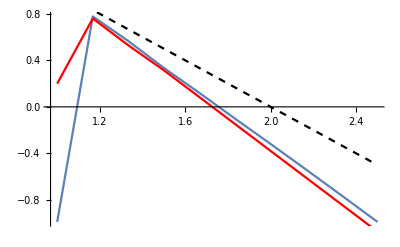

```mathematica
plt1 = ListLinePlot[Transpose[{ rvec,critomvec}], PlotRange->All];
plt2 = ListLinePlot[Transpose[{ rvec,2- rvec + sigma*critl1vec}], PlotRange->All, PlotStyle->Red];
plt3 = ListLinePlot[Transpose[{ rvec,2- rvec }], PlotRange->All, PlotStyle->{Black, Dashed}];
Show[plt1, plt2, plt3]
```

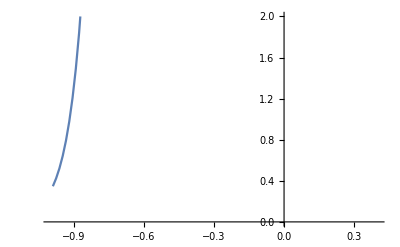

```mathematica
ListLinePlot[Transpose[{omvec, fvec}], PlotRange->{{-1,0.4},{0.0,2.0}}]
```

```mathematica
0.2^2
```

0.04

```mathematica
fvec2
```

{0.0305189,0.0319194,0.0334469,0.0352838,0.0370495,0.0471176,0.0416151,0.0456682,0.0463375,0.0495343,0.0547055,0.0590096,0.0676899,0.298853,0.0893306,0.183117,0.160572,2.64455,0.296703,0.580137,0.471713,0.691513,32.6281,1.71416,21.8659,4.75238,8.27293,299.576,12.2104,127.503,34.0672,117.534,58.5732,28322.6,76.7327,451.439,78.7081,740.633,229.971,244.291,3993.52,1459.06,338.963,3656.78,803.899,523.333,1117.74,1132.07,1110.79,8116.08,8116.08,1110.79,1132.07,1117.74,523.333,803.899,3656.78,338.963,1459.06,3993.52,244.291,229.971,740.633,78.7081,451.439,76.7327,28322.6,58.5732,117.534,34.0672,127.503,12.2104,299.576,8.27293,4.75238,21.8659,1.71416,32.6281,0.691513,0.471713,0.580137,0.296703,2.64455,0.160572,0.183117,0.0893306,0.298853,0.0676899,0.0590096,0.0547055,0.0495343,0.0463375,0.0456682,0.0416151,0.0471176,0.0370495,0.0352838,0.0334469,0.0319194,0.0305189}

```mathematica
N[critl1vec]
```

{-10.,-0.909091,-1.71717,-2.32323,-3.13131,-3.93939,-4.74747,-5.55556,-6.36364,-7.17172}